```mathematica
m=1.;α=0.2;n=64;tf=100.;p=2;
```

```mathematica
nsol=NDSolve[Evaluate@Flatten[{Table[m x[i]''[t]==(x[i + 1][t] - 2*x[i][t] + x[i - 1][t]) + α(x[i+1][t]-x[i]),{i,n}]/.{x[0][t]:>x[1][t]-1,x[n+1][t]:>x[n][t]+1},Table[{x[i][0]==i+RandomReal[{-.1,.1}]/2,x[i]'[0]==RandomReal[{-1,1}]},{i,n}]}],Table[x[i],{i,n}],{t,0,tf}];
```

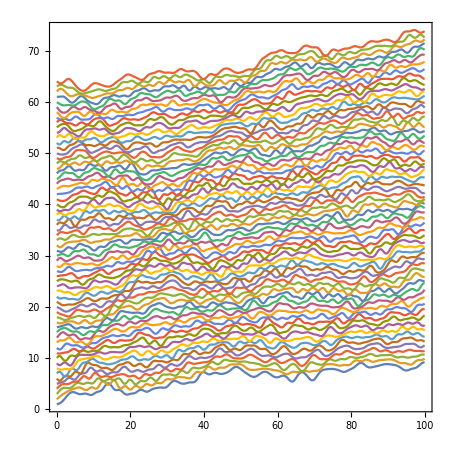

```mathematica
Plot[Evaluate[Table[x[i][t], {i, 1,n}] /. nsol], {t, 0, tf}, 
       PlotRange -> All,  Frame -> True, Axes -> False, 
       ImageSize -> 450, AspectRatio -> 1]
```